### Values of the steps for ℐ taken in the evaluation of the E_RMS

```mathematica
istep={20,10,5,2.5,1};
```

## Execution time (in seconds i) for each full RMS computation for both TSD4 formalisms (namely [0,0] and [1,0], respectively)

```mathematica
(*Subscript[T, 00],Subscript[T, 10]*)
durationParallel={{0.243,0.28},{2.589,2.643},{26.875,27.989},{263.387,291.802},{4299.52,4195.46}};
durationSerial={{1.792,1.936},{23.557,23.784},{212.835,201.771},{0,0},{0,0}};
```

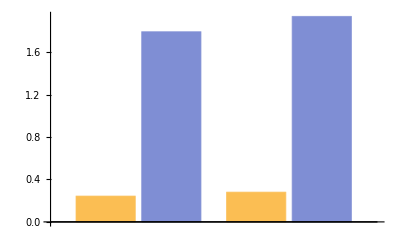

```mathematica
BarChart[{{durationParallel[[1,1]],durationSerial[[1,1]]},{durationParallel[[1,2]],durationSerial[[1,2]]}}]
```

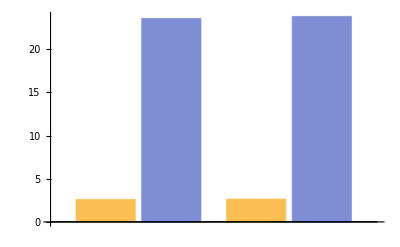

```mathematica
BarChart[{{durationParallel[[2,1]],durationSerial[[2,1]]},{durationParallel[[2,2]],durationSerial[[2,2]]}}]
```

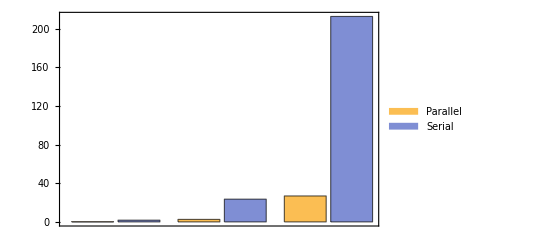

```mathematica
BarChart[{{durationParallel[[1,1]],durationSerial[[1,1]]},{durationParallel[[2,1]],durationSerial[[2,1]]},{durationParallel[[3,1]],durationSerial[[3,1]]}},ChartLegends->{"Parallel","Serial"},Frame->True]
```